```mathematica
SetOptions[ListPlot,BaseStyle->{FontSize->13}];
```

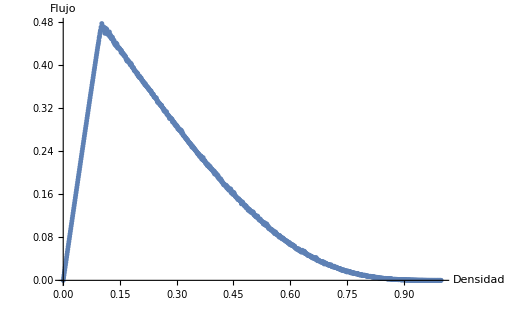

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_total.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Flujo"}]
```

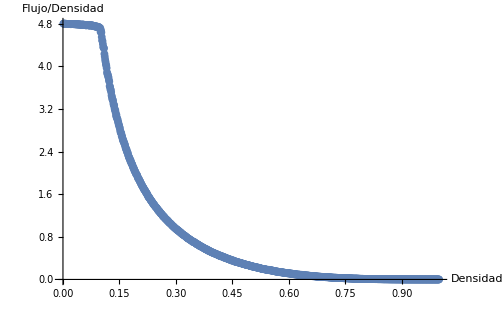

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_per_density_total.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Flujo/Densidad"}]
```

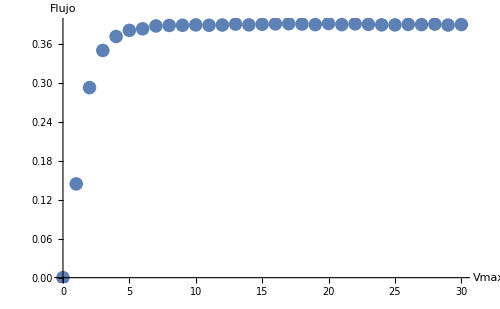

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\vmax_total.csv"];
ListPlot[data, AxesLabel->{"Vmax", "Flujo"}]
```

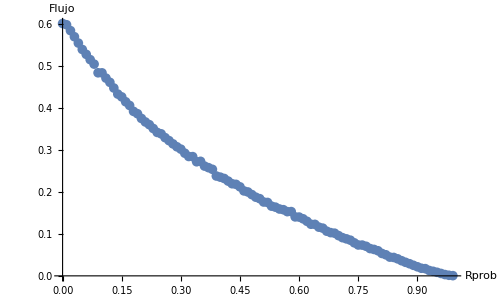

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_vs_rand_prob.csv"];
ListPlot[data, AxesLabel->{"Rprob", "Flujo"}]
```

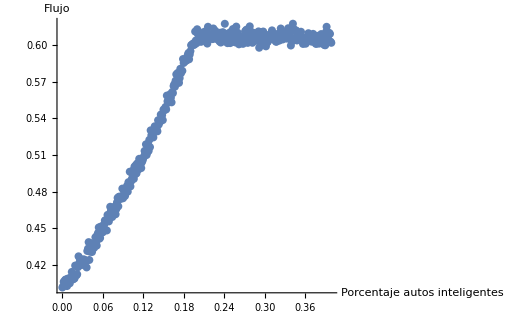

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Smart\\flow_vs_smart_car_density.csv"];
ListPlot[data, AxesLabel->{"Porcentaje \nautos inteligentes", "Flujo"}]
```

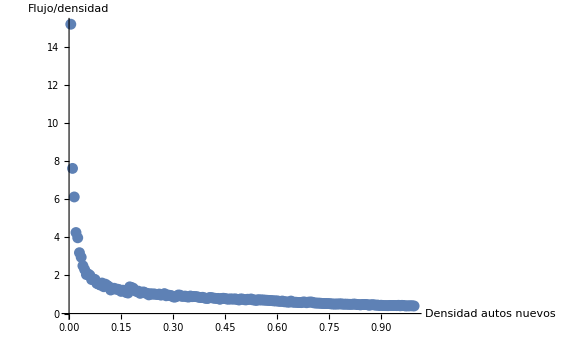

```mathematica
data = Import["E:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\FreewayAC\\Resultados\\Open\\flow_vs_smart_new_density.csv"];
ListPlot[data, AxesLabel->{"Densidad \nautos nuevos", "Flujo/densidad"},PlotRange->Full]
```

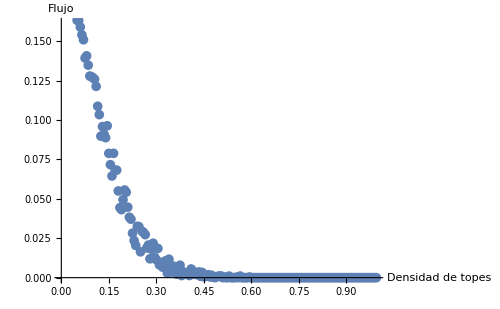

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Release\\flow_vs_stop_density.csv"];
ListPlot[data, AxesLabel->{"Densidad \nde topes", "Flujo"}, ImageSize->500]
```

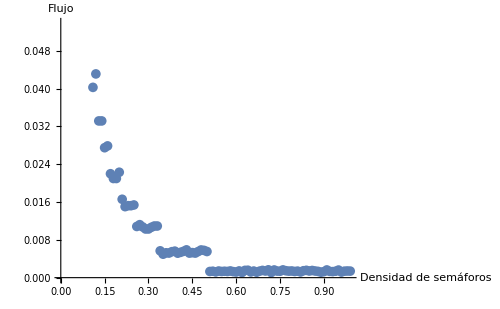

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Release\\flow_vs_semaphore_density.csv"];
ListPlot[data, AxesLabel->{"Densidad \nde semáforos", "Flujo"}, ImageSize->500]
```

```mathematica
(* Flow_vs_density var rand_prob *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/Resultados/Circular/3D_Flow_Vs_Density_Rand"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"Rp", "ρ", "q"}]
```

-Graphics3D-

```mathematica
(* Flow_vs_density var vmax *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/scripts"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"Vmax", "ρ", "q"}]
```

-Graphics3D-

```mathematica
(* Flow_vs_density var size *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/scripts"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"Size", "ρ", "q"}]
```

-Graphics3D-

```mathematica
(* Flow_vs_vmax var rand *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/scripts"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"rand", "vmax", "q"}]
```

-Graphics3D-

```mathematica
(* Flow_vs_smart var density *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/scripts"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"ρ", "ρ_smart", "q"}]
```

-Graphics3D-

```mathematica
(* Flow_vs_smart var rand *)
SetOptions[ListPlot3D,BaseStyle->{FontSize->12}];
SetDirectory["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/scripts"];
files=FileNames[];
For[i=1;csvFiles={};ex={},i≤Length[files],i++,If[FileExtension[files[[i]]]=="csv",(*Obtener valor de extra*)begin=Last[StringPosition[files[[i]],"_"]][[1]];
end=Last[StringPosition[files[[i]],"."]][[1]];
param=ToExpression[StringTake[files[[i]],{begin+1,end-1}]];
AppendTo[csvFiles,files[[i]]];
AppendTo[ex,param];
,False
]
]
csvFiles=csvFiles[[Ordering[ex]]];
ex=Sort[ex];
plt = {};
For[i=1,i≤Length[csvFiles],i++,
data = Import[csvFiles[[i]]];
For[j=1, j≤ Length[data], j++,
AppendTo[plt,{ex[[i]], data[[j]][[1]], data[[j]][[2]]}];
]
]
ListPlot3D[plt, AxesLabel->{"rand", "ρ_smart", "q"},PlotRange->Full]
```

-Graphics3D-

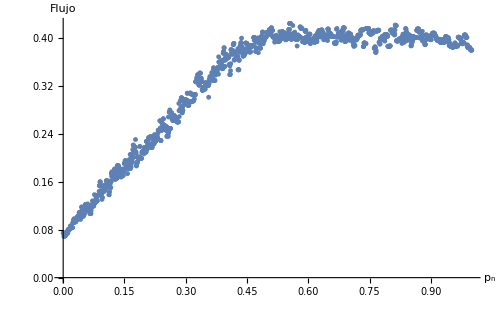

0.325779

```mathematica
(* Open *)
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Resultados\\Open\\flow_vs_new_car_prob.csv"];
ListPlot[data, AxesLabel->{"p_n", "Flujo"},ImageSize->500]
Mean[data[[All,2]][[2;;All]]]
```

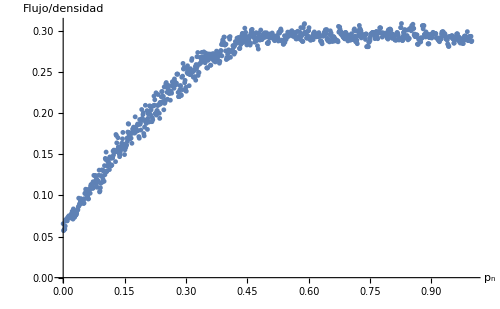

0.249828

```mathematica
(* Simple Junction *)
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Resultados\\SimpleJunction\\flow_vs_new_car_prob.csv"];
ListPlot[data, AxesLabel->{"p_n", "Flujo/densidad"},ImageSize->500]
Mean[data[[All,2]][[2;;All]]]
```

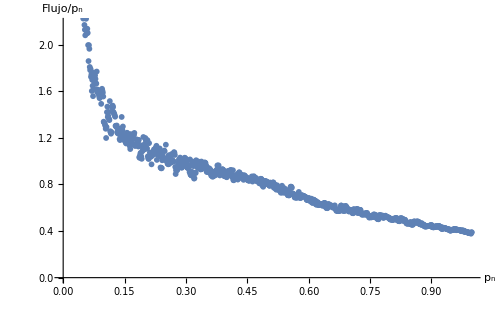

1.12373

```mathematica
(* Open *)
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Resultados\\Open\\flow_per_new_car_prob.csv"];
ListPlot[data, AxesLabel->{"p_n", "Flujo/p_n"},ImageSize->500]
Mean[data[[All,2]][[2;;All]]]
```

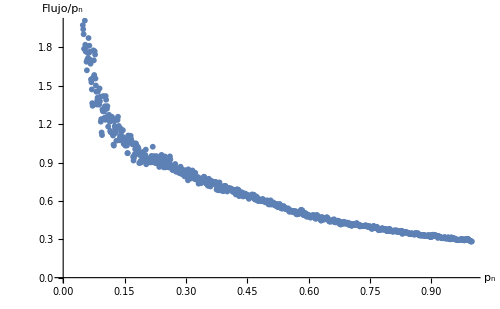

0.944279

```mathematica
(* Simple Junction *)
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Resultados\\SimpleJunction\\flow_per_new_car_prob.csv"];
ListPlot[data, AxesLabel->{"p_n", "Flujo/p_n"},ImageSize->500]
Mean[data[[All,2]][[2;;All]]]
```

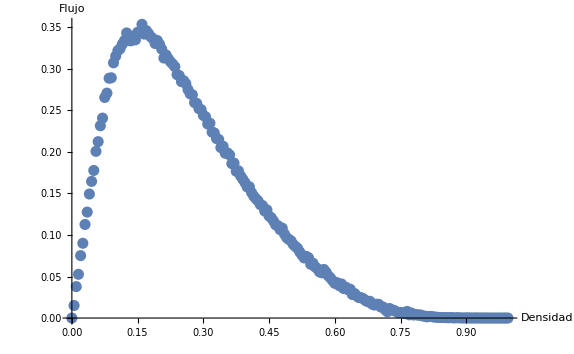

```mathematica
(* 2 Lane Circular *)
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinámicos\\FreewayAC\\Release\\flow_vs_density_multilane.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Flujo"}]
```

```mathematica
(* Dim Fractal *)
```

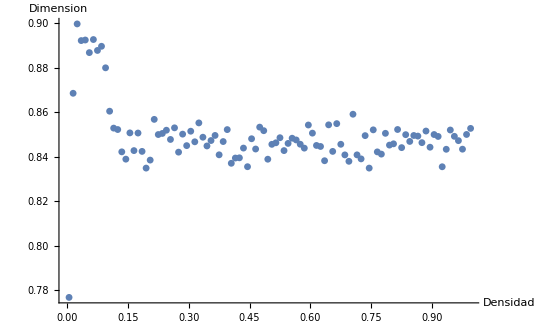

```mathematica
data = Import["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/Release/dimension_vs_density.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Dimension"},PlotRange->Full]
```

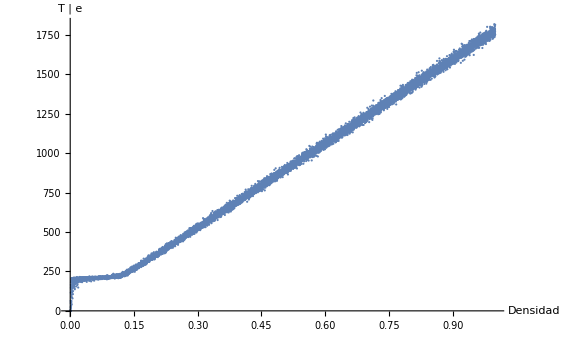

```mathematica
(* Tiempo de escape *)
data = Import["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/bin/escape_time_vs_density.csv"];
ListPlot[data, AxesLabel->{"Densidad", "T | e"}]
```

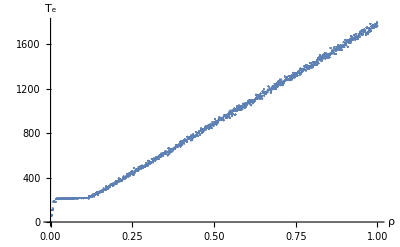

```mathematica
(* Misma semilla *)
data = Import["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/bin/escape_time_vs_density.csv"];
ListPlot[data, AxesLabel->{"ρ", "T_e"},ImageSize->400]
```

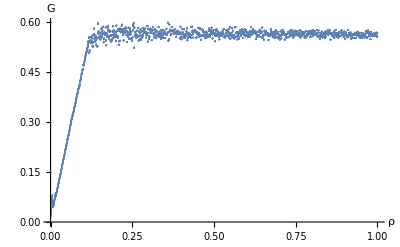

```mathematica
data = Import["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/bin/discharge_vs_density.csv"];
ListPlot[data, AxesLabel->{"ρ", "G"},ImageSize->400, PlotRange->Full]
```

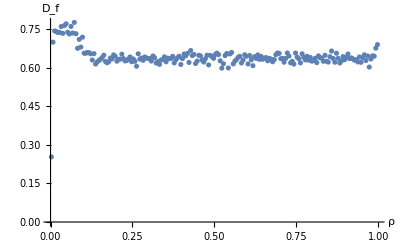

```mathematica
data=Import["/home/carlos/Documentos/Maestria/Sistemas_Dinamicos/FreewayAC/bin/dimension_vs_density.csv"];
ListPlot[data,PlotRange->Full,ImageSize->400, AxesLabel->{"ρ", "D_f"}]
```